```mathematica
HH[Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,qa_,qb_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=1/4 (2 hz Cos[θ1]+2 hz Cos[θ2]-2 hz Cos[θ3]-(J+Kz) Cos[θ2] Cos[θ3]-2 hz Cos[θ4]+2 hx Cos[ϕ1] Sin[θ1]+Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+2 hx Cos[ϕ2] Sin[θ2]+Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]-2 hx Cos[ϕ3] Sin[θ3]+Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])-2 hx Cos[ϕ4] Sin[θ4]+Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]+2 hy Sin[θ1] Sin[ϕ1]+2 hy Sin[θ2] Sin[ϕ2]+(J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]-Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])+ⅇ^(-ⅈ qb) (Cos[θ1] (J Cos[θ2]+Γxy Sin[θ2] Sin[ϕ2])+Sin[θ1] ((J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ2]+Sin[ϕ1] (Γxy Cos[θ2]+J Sin[θ2] Sin[ϕ2])))-2 hy Sin[θ3] Sin[ϕ3]-Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]-2 hy Sin[θ4] Sin[ϕ4]+(J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[θ3] (J Cos[θ4]+Γxy Sin[θ4] Sin[ϕ4])+Sin[θ3] ((J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ4]+Sin[ϕ3] (Γxy Cos[θ4]+J Sin[θ4] Sin[ϕ4])))+ⅇ^(-ⅈ (qa+qb)) (-(J+Kz) Cos[θ1] Cos[θ4]-Sin[θ1] Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])))
pKxy=-6.8;
pKz=−6.8;
pΓxy=9.5;
pΓz=9.5;
pJ=0;
phx=2.7;
phy=0;
phz=0;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;

ff[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=HH[pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,0,0,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
{a,b}=FindMinimum[{ff[θ[1],θ[2],θ[3],θ[4],ϕ[1],ϕ[2],ϕ[3],ϕ[4]],0<θ[1]<Pi&&0<θ[2]<Pi&&0<θ[3]<Pi&&0<θ[4]<Pi&&0<ϕ[1]<2Pi&&0<ϕ[2]<2Pi&&0<ϕ[3]<2Pi&&0<ϕ[4]<2Pi},{{θ[1],pθ+0.8},{θ[2],pθ-0.8},{θ[3],pθ+0.5},{θ[4],pθ-0.5},{ϕ[1],pϕ+0.5},{ϕ[2],pϕ-0.5},{ϕ[3],pϕ+0.8},{ϕ[4],pϕ-0.8}}];
```

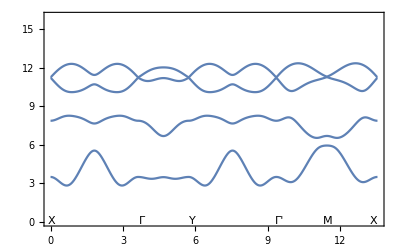

```mathematica
For[i=1,i≤4,i++,{ppθ[i]=θ[i]/.b[[i]],ppϕ[i]=ϕ[i]/.b[[i+4]]}]
Hh[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})

HHh[qa_,qb_]:=Hh[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]

EE[qa_,qb_]:=Sort[Eigenvalues[HHh[qa,qb]]]

Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/Sqrt[3]+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

### The one direction hopping matrix within one a lay

```mathematica
DDH[qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=({{-(hz Cos[θ1]+1/2 (-J-Kz) Cos[θ1] Cos[θ4]+hx Cos[ϕ1] Sin[θ1]+1/2 Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+1/2 (J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ1] Sin[θ2]+1/2 Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]+hy Sin[θ1] Sin[ϕ1]-1/2 Cos[ϕ4] Sin[θ1] Sin[θ4] (J Cos[ϕ1]+Γz Sin[ϕ1])+1/2 Cos[θ2] (J Cos[θ1]+Γxy Sin[θ1] Sin[ϕ1])+1/2 (J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]+1/2 Sin[θ2] (Γxy Cos[θ1]+J Sin[θ1] Sin[ϕ1]) Sin[ϕ2]-1/2 Sin[θ1] Sin[θ4] (Γz Cos[ϕ1]+J Sin[ϕ1]) Sin[ϕ4]), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, 0, 0}, {0, -(hz Cos[θ1]+1/2 (-J-Kz) Cos[θ1] Cos[θ4]+hx Cos[ϕ1] Sin[θ1]+1/2 Cos[θ2] (J Cos[θ1]+Γxy Cos[ϕ1] Sin[θ1])+1/2 (J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ1] Sin[θ2]+1/2 Cos[ϕ2] (Γxy Cos[θ1]+J Cos[ϕ1] Sin[θ1]) Sin[θ2]+hy Sin[θ1] Sin[ϕ1]-1/2 Cos[ϕ4] Sin[θ1] Sin[θ4] (J Cos[ϕ1]+Γz Sin[ϕ1])+1/2 Cos[θ2] (J Cos[θ1]+Γxy Sin[θ1] Sin[ϕ1])+1/2 (J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]+1/2 Sin[θ2] (Γxy Cos[θ1]+J Sin[θ1] Sin[ϕ1]) Sin[ϕ2]-1/2 Sin[θ1] Sin[θ4] (Γz Cos[ϕ1]+J Sin[ϕ1]) Sin[ϕ4]), (-J-Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, 0, 0}, {0, 0, -(hz Cos[θ2]+J Cos[θ1] Cos[θ2]-1/2 (J+Kz) Cos[θ2] Cos[θ3]+1/2 Γxy Cos[θ2] Cos[ϕ1] Sin[θ1]+hx Cos[ϕ2] Sin[θ2]+1/2 (J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ1] Sin[θ2]+Cos[ϕ2] (1/2 Γxy Cos[θ1]+1/2 J Cos[ϕ1] Sin[θ1]) Sin[θ2]+1/2 Γxy Cos[θ2] Sin[θ1] Sin[ϕ1]+hy Sin[θ2] Sin[ϕ2]+1/2 (J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]+Sin[θ2] (1/2 Γxy Cos[θ1]+1/2 J Sin[θ1] Sin[ϕ1]) Sin[ϕ2]-1/2 Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])-1/2 Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {0, 0, 0, -(hz Cos[θ2]+J Cos[θ1] Cos[θ2]-1/2 (J+Kz) Cos[θ2] Cos[θ3]+1/2 Γxy Cos[θ2] Cos[ϕ1] Sin[θ1]+hx Cos[ϕ2] Sin[θ2]+1/2 (J+Kxy) Cos[ϕ1] Cos[ϕ2] Sin[θ1] Sin[θ2]+Cos[ϕ2] (1/2 Γxy Cos[θ1]+1/2 J Cos[ϕ1] Sin[θ1]) Sin[θ2]+1/2 Γxy Cos[θ2] Sin[θ1] Sin[ϕ1]+hy Sin[θ2] Sin[ϕ2]+1/2 (J+Kxy) Sin[θ1] Sin[θ2] Sin[ϕ1] Sin[ϕ2]+Sin[θ2] (1/2 Γxy Cos[θ1]+1/2 J Sin[θ1] Sin[ϕ1]) Sin[ϕ2]-1/2 Cos[ϕ3] Sin[θ2] Sin[θ3] (J Cos[ϕ2]+Γz Sin[ϕ2])-1/2 Sin[θ2] Sin[θ3] (Γz Cos[ϕ2]+J Sin[ϕ2]) Sin[ϕ3]), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, 0, 0, -(-hz Cos[θ3]-1/2 (J+Kz) Cos[θ2] Cos[θ3]-hx Cos[ϕ3] Sin[θ3]+1/2 Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])+1/2 (J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ3] Sin[θ4]+1/2 Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]-Cos[ϕ3] Sin[θ3] (1/2 J Cos[ϕ2] Sin[θ2]+1/2 Γz Sin[θ2] Sin[ϕ2])-hy Sin[θ3] Sin[ϕ3]-Sin[θ3] (1/2 Γz Cos[ϕ2] Sin[θ2]+1/2 J Sin[θ2] Sin[ϕ2]) Sin[ϕ3]+1/2 Cos[θ4] (J Cos[θ3]+Γxy Sin[θ3] Sin[ϕ3])+1/2 (J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+1/2 Sin[θ4] (Γxy Cos[θ3]+J Sin[θ3] Sin[ϕ3]) Sin[ϕ4]), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) ((-J-Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, 0, 0, 0, -(-hz Cos[θ3]-1/2 (J+Kz) Cos[θ2] Cos[θ3]-hx Cos[ϕ3] Sin[θ3]+1/2 Cos[θ4] (J Cos[θ3]+Γxy Cos[ϕ3] Sin[θ3])+1/2 (J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ3] Sin[θ4]+1/2 Cos[ϕ4] (Γxy Cos[θ3]+J Cos[ϕ3] Sin[θ3]) Sin[θ4]-Cos[ϕ3] Sin[θ3] (1/2 J Cos[ϕ2] Sin[θ2]+1/2 Γz Sin[θ2] Sin[ϕ2])-hy Sin[θ3] Sin[ϕ3]-Sin[θ3] (1/2 Γz Cos[ϕ2] Sin[θ2]+1/2 J Sin[θ2] Sin[ϕ2]) Sin[ϕ3]+1/2 Cos[θ4] (J Cos[θ3]+Γxy Sin[θ3] Sin[ϕ3])+1/2 (J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+1/2 Sin[θ4] (Γxy Cos[θ3]+J Sin[θ3] Sin[ϕ3]) Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {0, 0, 0, 0, 0, 0, -(-hz Cos[θ4]+1/2 (-J-Kz) Cos[θ1] Cos[θ4]+J Cos[θ3] Cos[θ4]+1/2 Γxy Cos[θ4] Cos[ϕ3] Sin[θ3]-hx Cos[ϕ4] Sin[θ4]+1/2 (J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ3] Sin[θ4]+Cos[ϕ4] (1/2 Γxy Cos[θ3]+1/2 J Cos[ϕ3] Sin[θ3]) Sin[θ4]-Cos[ϕ4] Sin[θ4] (1/2 J Cos[ϕ1] Sin[θ1]+1/2 Γz Sin[θ1] Sin[ϕ1])+1/2 Γxy Cos[θ4] Sin[θ3] Sin[ϕ3]-hy Sin[θ4] Sin[ϕ4]-Sin[θ4] (1/2 Γz Cos[ϕ1] Sin[θ1]+1/2 J Sin[θ1] Sin[ϕ1]) Sin[ϕ4]+1/2 (J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+Sin[θ4] (1/2 Γxy Cos[θ3]+1/2 J Sin[θ3] Sin[ϕ3]) Sin[ϕ4]), 0}, {0, 0, 0, 0, 0, 0, 0, -(-hz Cos[θ4]+1/2 (-J-Kz) Cos[θ1] Cos[θ4]+J Cos[θ3] Cos[θ4]+1/2 Γxy Cos[θ4] Cos[ϕ3] Sin[θ3]-hx Cos[ϕ4] Sin[θ4]+1/2 (J+Kxy) Cos[ϕ3] Cos[ϕ4] Sin[θ3] Sin[θ4]+Cos[ϕ4] (1/2 Γxy Cos[θ3]+1/2 J Cos[ϕ3] Sin[θ3]) Sin[θ4]-Cos[ϕ4] Sin[θ4] (1/2 J Cos[ϕ1] Sin[θ1]+1/2 Γz Sin[θ1] Sin[ϕ1])+1/2 Γxy Cos[θ4] Sin[θ3] Sin[ϕ3]-hy Sin[θ4] Sin[ϕ4]-Sin[θ4] (1/2 Γz Cos[ϕ1] Sin[θ1]+1/2 J Sin[θ1] Sin[ϕ1]) Sin[ϕ4]+1/2 (J+Kxy) Sin[θ3] Sin[θ4] Sin[ϕ3] Sin[ϕ4]+Sin[θ4] (1/2 Γxy Cos[θ3]+1/2 J Sin[θ3] Sin[ϕ3]) Sin[ϕ4])}})
```

### The one direction hopping matrix within a and a+1 layer

```mathematica
ODM[qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {ⅇ^(ⅈ qb) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ qb) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, 0, 0, 0, 0}, {ⅇ^(ⅈ qb) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ qb) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, 0, 0, 0, 0}});
```

### Constructing Final Hamiltonian

```mathematica
Clear[i,j1,j2];
layNum=30;
```

```mathematica
UPHM=DDH[qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]];
ODMM=ODM[qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]];
LHHM=Table[0,{i,8layNum},{j,8layNum}];(*Define large half matrix as all zero with lay Numember as layNum*)
For[i=1,i≤layNum,i++,For[j1=1,j1≤8,j1++,For[j2=j1,j2≤8,j2++,LHHM[[(i-1)*8+j1]][[(i-1)*8+j2]]=UPHM[[j1]][[j2]]]]];
For[i=1,i≤layNum-1,i++,For[j1=7,j1≤8,j1++,For[j2=1,j2≤2,j2++,LHHM[[(i-1)*8+j1]][[(i)*8+j2]]=ODMM[[j1]][[j2]]]]];
LFH=LHHM+Simplify[ConjugateTranspose[LHHM],Assumptions->Element[qb,Reals]];
largeSigmaY=KroneckerProduct[IdentityMatrix[4*layNum],PauliMatrix[2]];
EOM=(1/2)*largeSigmaY.LFH;
MatrixForm[EOM]
```

```mathematica
HEOM[qb_]:=({{0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+4.596632700768215 ⅈ, 0.+0.33018347133805614 ⅈ, 0.+12.556899327485732 ⅈ, 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (0.8657139614009735-9.1638510459589 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (5.604926246242762-0.21910968734395295 ⅇ^(ⅈ qb))), 0., 0.-12.556899327478988 ⅈ, 1/2 (0.+(0.+0.7461844170239591 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-6.758930313082454-0.04106968691754659 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(ⅈ qb))), 0.+12.556899327478988 ⅈ, 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(ⅈ qb)), 1/2 (0.+(0.+0.6603669426628781 ⅈ) ⅇ^(ⅈ qb)), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-(0.+0.6603669426628781 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.+(0.+5.420796671284851 ⅈ) ⅇ^(-ⅈ qb)), 0., 0.-9.54011730607964 ⅈ, 1/2 (0.-ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+(0.+9.19326540155094 ⅈ) ⅇ^(-ⅈ qb)), 1/2 (0.-(0.+0.7461844170239591 ⅈ) ⅇ^(-ⅈ qb)), 0.+9.54011730607964 ⅈ, 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(-ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(-ⅈ qb))), 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.-ⅈ (-8.663850265500438-1.9330404026435462 ⅇ^(ⅈ qb))), 1/2 (0.-ⅈ (-1.3880263731747893+4.941871401386466 ⅇ^(ⅈ qb))), 0., 0.-9.540117306074418 ⅈ, 0.-0.33018347133805614 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 1/2 (0.+ⅈ (-0.21085135483912615-6.589148645160874 ⅇ^(ⅈ qb))), 1/2 (0.+ⅈ (-8.663850265511345-1.9330404026148846 ⅇ^(ⅈ qb))), 0.+9.540117306074418 ⅈ, 0., 0.+4.596632700768215 ⅈ, 0.-0.37309220851577257 ⅈ, 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.+0.37309220851577257 ⅈ, 0.+2.7103983356546957 ⅈ, 0., 0.-12.556899327485732 ⅈ, 1/2 (0.-ⅈ (0.8657139613297922-9.163851045955004 ⅇ^(-ⅈ qb))), 1/2 (0.-ⅈ (5.604926246
```

```mathematica
EEOM[qb_]:=Sort[Re[Eigenvalues[HEOM[qb]]]]
ESYS[qb_]:=Eigensystem[HEOM[qb]]
```

### Color function for given bands left edge is red, right edge is green, bulk is blue

```mathematica
cf[eve_,bln_]:=Module[{a,b,c,le,re,nor},nor=Norm[eve];le=Norm[eve[[Range[bln]]]]/nor;re=Norm[eve[[Range[Length[eve]-bln+1,Length[eve]]]]]/nor;If[le>0.5,a=1;b=0;c=0,If[re>0.5,a=0;b=1;c=0,a=0;b=0;c=1]];{a,b,c}]
```

### Different bands data

```mathematica
plotN=200;
bln=12;
```

```mathematica
bandsdata=Table[ESYS[(n-1)*(2Pi)/plotN],{n,plotN+1}];
```

```mathematica
bandsdata[[1]][[2]][[2]]
```

```mathematica
timebands={Table[0,{n,layNum*8}],Table[0,{n,layNum*8},{m,layNum*8}]};
For[i=1,i≤plotN+1,i++,timebands=bandsdata[[i]];timebands[[1]]=Re[timebands[[1]]];bandsdata[[i]][[1]]=Sort[timebands[[1]],Greater][[Range[4*layNum]]];For[j=1,j≤layNum*4,j++,{{posi}}=Position[timebands[[1]],bandsdata[[i]][[1]][[j]]];bandsdata[[i]][[2]][[j]]=timebands[[2]][[posi]]];bandsdata[[i]][[2]]=bandsdata[[i]][[2]][[Range[4*layNum]]]];
bandF[x_,n_]:=bandsdata[[x]][[1]][[n]];
eveF[x_,n_]:=bandsdata[[x]][[2]][[n]];
```

```mathematica
bandF[1,60]
```

10.9491

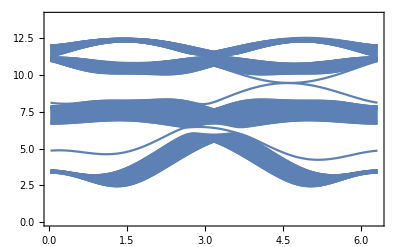

```mathematica
Show[Table[DiscretePlot[bandF[x*100/Pi,n],{x,1*Pi/100,(plotN+1)*Pi/100,Pi/100},Filling->None,Joined->True,PlotRange->{{1*Pi/100,(plotN+1)*Pi/100},{0,14}},ColorFunctionScaling->False,Frame->True,ColorFunction->Function[{xx,yy},RGBColor[cf[eveF[xx*100/Pi,n],bln]]]],{n,layNum*4}]]
```

### Chern number

#### square root of a matrix

```mathematica
MH[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,J_,hx_,hy_,hz_,θ1_,ϕ1_,θ2_,ϕ2_,θ3_,ϕ3_,θ4_,ϕ4_]:=({{-Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, (J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(-ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4])}, {0, -Cos[θ1] (2 hz+2 J Cos[θ2]-(J+Kz) Cos[θ4]+Γxy Sin[θ2] (Cos[ϕ2]+Sin[ϕ2]))-Sin[θ1] (2 hx Cos[ϕ1]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ2]+2 hy Sin[ϕ1]+Γxy Cos[θ2] (Cos[ϕ1]+Sin[ϕ1])-Sin[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(-ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(-ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, 0, ⅇ^(-ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]))}, {(J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (J Cos[ϕ1] Cos[ϕ2]+(J+Kxy) Sin[ϕ1] Sin[ϕ2]), -(J+Kxy) Cos[θ1] Cos[ϕ2] Sin[ϕ1]+(J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1]) Sin[ϕ2]+ⅇ^(ⅈ qb) (Cos[ϕ2] (Γxy Sin[θ1]-J Cos[θ1] Sin[ϕ1])+(J+Kxy) Cos[θ1] Cos[ϕ1] Sin[ϕ2]), -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), 0, 0}, {J Cos[θ2] Cos[ϕ2] Sin[ϕ1]-Γxy Sin[θ2] Sin[ϕ1]-(J+Kxy) Cos[θ2] Cos[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) ((J+Kxy) Cos[θ2] Cos[ϕ2] Sin[ϕ1]+Cos[ϕ1] (Γxy Sin[θ2]-J Cos[θ2] Sin[ϕ2])), Cos[θ2] Cos[ϕ2] (J Cos[θ1] Cos[ϕ1]-Γxy Sin[θ1])-Γxy Cos[θ1] Cos[ϕ1] Sin[θ2]+J Sin[θ1] Sin[θ2]+(J+Kxy) Cos[θ1] Cos[θ2] Sin[ϕ1] Sin[ϕ2]+ⅇ^(ⅈ qb) (Sin[θ1] (J Sin[θ2]-Γxy Cos[θ2] Sin[ϕ2])+Cos[θ1] (-Γxy Sin[θ2] Sin[ϕ1]+Cos[θ2] ((J+Kxy) Cos[ϕ1] Cos[ϕ2]+J Sin[ϕ1] Sin[ϕ2]))), 0, -Cos[θ2] (2 hz+2 J Cos[θ1]-(J+Kz) Cos[θ3]+Γxy Sin[θ1] (Cos[ϕ1]+Sin[ϕ1]))-Sin[θ2] (2 hx Cos[ϕ2]+(2 J+Kxy) Cos[ϕ1-ϕ2] Sin[θ1]+2 hy Sin[ϕ2]+Γxy Cos[θ1] (Cos[ϕ2]+Sin[ϕ2])-Sin[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3])), Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, 0}, {0, 0, -J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3], Cos[θ2] (Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4]))}, {0, 0, Cos[θ3] (-Γz Cos[ϕ2+ϕ3]+J Sin[ϕ2-ϕ3]), (J+Kz) Sin[θ2] Sin[θ3]+Cos[θ2] Cos[θ3] (J Cos[ϕ2-ϕ3]+Γz Sin[ϕ2+ϕ3]), 0, Sin[θ3] (2 hx Cos[ϕ3]+J Cos[ϕ2-ϕ3] Sin[θ2]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ4]+2 hy Sin[ϕ3]-Γxy Cos[θ4] (Cos[ϕ3]+Sin[ϕ3])+Γz Sin[θ2] Sin[ϕ2+ϕ3])+Cos[θ3] (2 hz+(J+Kz) Cos[θ2]-2 J Cos[θ4]-Γxy Sin[θ4] (Cos[ϕ4]+Sin[ϕ4])), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(-ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(-ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4])))}, {ⅇ^(ⅈ (qa+qb)) (-J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4]), ⅇ^(ⅈ (qa+qb)) Cos[θ1] (Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), 0, 0, (J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (J Cos[ϕ3] Cos[ϕ4]+(J+Kxy) Sin[ϕ3] Sin[ϕ4]), (J+Kxy) Cos[θ3] Cos[ϕ4] Sin[ϕ3]+(-J Cos[θ3] Cos[ϕ3]+Γxy Sin[θ3]) Sin[ϕ4]+ⅇ^(ⅈ qb) (Cos[ϕ4] (-Γxy Sin[θ3]+J Cos[θ3] Sin[ϕ3])-(J+Kxy) Cos[θ3] Cos[ϕ3] Sin[ϕ4]), Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4]), 0}, {ⅇ^(ⅈ (qa+qb)) Cos[θ4] (-Γz Cos[ϕ1+ϕ4]+J Sin[ϕ1-ϕ4]), ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ1] Sin[θ4]+Cos[θ1] Cos[θ4] (J Cos[ϕ1-ϕ4]+Γz Sin[ϕ1+ϕ4])), 0, 0, -J Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Γxy Sin[θ4] Sin[ϕ3]+(J+Kxy) Cos[θ4] Cos[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (-(J+Kxy) Cos[θ4] Cos[ϕ4] Sin[ϕ3]+Cos[ϕ3] (-Γxy Sin[θ4]+J Cos[θ4] Sin[ϕ4])), Cos[θ4] Cos[ϕ4] (J Cos[θ3] Cos[ϕ3]-Γxy Sin[θ3])-Γxy Cos[θ3] Cos[ϕ3] Sin[θ4]+J Sin[θ3] Sin[θ4]+(J+Kxy) Cos[θ3] Cos[θ4] Sin[ϕ3] Sin[ϕ4]+ⅇ^(ⅈ qb) (Sin[θ3] (J Sin[θ4]-Γxy Cos[θ4] Sin[ϕ4])+Cos[θ3] (-Γxy Sin[θ4] Sin[ϕ3]+Cos[θ4] ((J+Kxy) Cos[ϕ3] Cos[ϕ4]+J Sin[ϕ3] Sin[ϕ4]))), 0, Cos[θ4] (2 hz+(J+Kz) Cos[θ1]-2 J Cos[θ3]-Γxy Sin[θ3] (Cos[ϕ3]+Sin[ϕ3]))+Sin[θ4] (2 hx Cos[ϕ4]+J Cos[ϕ1-ϕ4] Sin[θ1]-(2 J+Kxy) Cos[ϕ3-ϕ4] Sin[θ3]+2 hy Sin[ϕ4]-Γxy Cos[θ3] (Cos[ϕ4]+Sin[ϕ4])+Γz Sin[θ1] Sin[ϕ1+ϕ4])}})
MMH[qa_,qb_]:=MH[qa,qb,pKxy,pKz,pΓxy,pΓz,pJ,phx,phy,phz,ppθ[1],ppϕ[1],ppθ[2],ppϕ[2],ppθ[3],ppϕ[3],ppθ[4],ppϕ[4]]
SRM[qa_,qb_]:=MatrixPower[MMH[qa,qb],1/2]
FH[qa_,qb_]:=(1/2)SRM[qa,qb].({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).SRM[qa,qb]
EEM[qa_,qb_]:=Sort[Eigenvalues[FH[qa,qb]]]
```

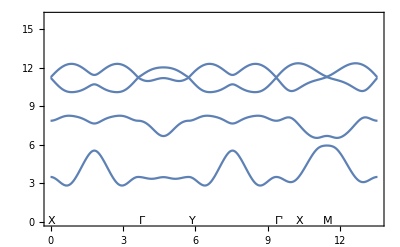

```mathematica
Plot[Piecewise[{{EEM[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EEM[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EEM[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EEM[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EEM[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/3+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,16}}]
```

#### Calculate the chern numberp

1.eigenvector of fermion hamiltonian

2. Phases difference of two given vectors, and the order matters.

3. The field strength per plaquette

4. the chern number for given discrete number DN, nthband is the band with nth large eigenvalues

```mathematica
nthband=6;
DN=40;
vec[qa_,qb_]:=Module[{eve,eva,p},{eva,eve}=Eigensystem[FH[qa,qb]];
                                     {{p}}=Position[eva,Sort[eva][[nthband]]];
                                      eve[[p]]]
pd[v1_,v2_]:=(Conjugate[v1].v2)/Abs[Conjugate[v1].v2]
fs[qa_,qb_,dk_]:=Re[Log[pd[vec[qa,qb],vec[qa+dk,qb]]*pd[vec[qa+dk,qb],vec[qa+dk,qb+dk]]*pd[vec[qa+dk,qb+dk],vec[qa,qb+dk]]*pd[vec[qa,qb+dk],vec[qa,qb]]]/I]
CN=0;
dk=2*Pi/DN;
For[i=0,i<DN,i++,
For[j=0,j<DN,j++,
CN=CN+fs[2*Pi*i/DN,2*Pi*j/DN,dk];]]
CN/(2Pi)
```

1.

#### pKxy=-6.8; pKz=−6.8; pΓxy=9.5; pΓz=9.5; pJ=0.1724202958; is critical value for c=0 and c=-1 PJ=0.7 ; is the other critical value between c=-1 and c=0 therefore choose pJ=0.45 can maximum the gap phx=-0.5; phy=0.45; phz=1.2;

### Fermion OBC spectrum

```mathematica
NNN=30;
FMMH[i_,qb_]:=(1/(2*NNN))Sum[FH[kx,qb]*Exp[-I kx i],{kx,0,2Pi-2Pi/(2*NNN),2Pi/(2*NNN)}]
FMOBH[qb_]:=Module[{m},m=Table[0,{a,NNN},{b,NNN}];For[i=1,i≤NNN,i++,For[j=1,j≤NNN,j++,m[[i]][[j]]=FMMH[j-i,qb]]];ArrayFlatten[m]]
```